```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/ninel/Documents/potts/potts

```mathematica
list=FileNames["./output/ctags*.out","",2];
```

```mathematica
data=Import["./output/ctags"<>ToString[100]<>".out","Table"];
```

```mathematica
CQ[list_]:=Module[{c=list,pos},pos=Position[c,1];
If[c[[2,2]]==1&&Length@pos>2,0,c[[2,2]]]];
```

```mathematica
DeleteCentral[x_]:=Module[{c=ArrayPad[x,1],w,l},{w,l}=Dimensions[x];
Table[CQ[c[[i-1;;i+1,j-1;;j+1]]],{i,2,w+1},{j,2,l+1}]]
```

```mathematica
CountLegs[gr_]:=Module[{mc=MorphologicalComponents[Image[DeleteCentral[Map[If[#>0,1,0]&,ImageData@SkeletonTransform[ColorNegate@gr],{2}]]]]},Max[mc]];
```

```mathematica
Sort[DeleteDuplicates[Flatten@data]] //Last
```

98

```mathematica
M=800
```

800

```mathematica
hue[x_]:=If[x==0,{0,0,0},{Piecewise[{{2-6x, 1/6<x≤2/6}, {0, 2/6<x≤4/6}, {6x-4, 4/6<x≤5/6}, {1, True}}],Piecewise[{{6x, 0/6<x≤1/6}, {1, 1/6<x≤3/6}, {4-6x, 3/6<x≤4/6}, {0, True}}],Piecewise[{{0, 0/6<x≤2/6}, {6x-2, 2/6<x≤3/6}, {6-6x, 5/6<x≤6/6}, {1, True}}]}];
```

```mathematica
permute=RandomSample[Range[M]];
```

```mathematica
changes=Table[i-> permute[[i]],{i,1,M}];
```

```mathematica
permute2=RandomSample[Range[M]];
changes2=Table[i-> permute2[[i]],{i,1,M}];
```

```mathematica
(*{1,1,1}(0.6(x/.changes)/M+If[x==0,0,0.4])-{0.3,0.3,0.3}hue[(x/.changes2)/M]*)
```

```mathematica
(*data=Import["./output/ctags"<>ToString[100#]<>".out","Table"]&/@Range[12];*)
```

```mathematica
(*ImageAssemble@Partition[Map[Image[Map[ColorsReplace,#,{2}]ᵀ]&,data],3]*)
```

```mathematica
Clear[ColorsReplace]
ColorsReplace[x_]:=(ColorsReplace[x]=Piecewise[{{{0,0,0}, x==0}, {{0,1,0}(1/3+2/3(x/.changes)/M)+{1/3,0,0}((x/.changes2)/M), types[[x]]==1}, {{0,0,1}(1/3+2/3(x/.changes)/M)+{1/3,0,0}((x/.changes2)/M), True}}])
```

```mathematica
fibersI=Import["./output/fib.out","Table"];
types=First@Import["./output/types.out","Table"];
```

```mathematica
indexes=Import["./output/ctags"<>ToString[900]<>".out","Table"];
```

```mathematica
Image[Map[ColorsReplace,indexes,{2}]ᵀ+Map[0.1{#,#,#}&,fibersI,{2}]ᵀ]
```

-Graphics-

```mathematica
Dimensions[indexes]
```

{480,480}

```mathematica
400 400/160
```

1000

```mathematica
√1000//N
```

31.6228

```mathematica
legsC=Table[Module[{mCell=Map[If[#==n,0,1]&,indexes,{2}]},{n,CountLegs[ImageCrop@Image[mCellᵀ]],types[[n]]}],{n,1,Length@types-1}]
```

{{1,6,2},{2,11,2},{3,7,2},{4,7,2},{5,12,2},{6,6,2},{7,9,2},{8,8,2},{9,10,2},{10,7,2},{11,11,2},{12,9,2},{13,10,2},{14,6,2},{15,10,2},{16,7,2},{17,6,2},{18,8,2},{19,10,2},{20,10,2},{21,10,2},{22,9,2},{23,7,2},{24,10,2},{25,6,2},{26,11,2},{27,7,2},{28,10,2},{29,9,2},{30,7,2},{31,6,2},{32,7,2},{33,6,2},{34,9,2},{35,5,2},{36,10,2},{37,12,2},{38,8,2},{39,5,2},{40,10,2},{41,10,2},{42,7,2},{43,6,2},{44,7,2},{45,10,2},{46,10,2},{47,6,2},{48,6,2}}

```mathematica
legsCM=Select[legsC,#[[3]]==1&][[;;,2]];
legsFB=Select[legsC,#[[3]]==2&][[;;,2]];
```

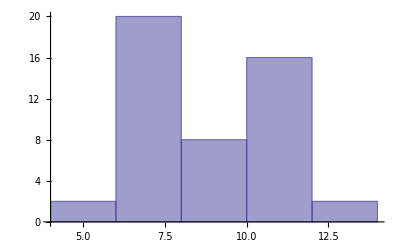

{Mean[{}],8.25}

StandardDeviation::shlen: The argument {} should have at least two elements.

{StandardDeviation[{}],1.96241}

```mathematica
Histogram[{legsCM,legsFB}]
Mean/@{legsCM,legsFB}//N
StandardDeviation/@{legsCM,legsFB}//N
```

```mathematica
mCM=Map[If[#>0&&types[[#]]==1,#,0]&,indexes,{2}];
mFB=Map[If[#>0&&types[[#]]==2,#,0]&,indexes,{2}];
```

```mathematica
mCMᵀ//Colorize
```

-Graphics-

```mathematica
mFBᵀ//Colorize
```

-Graphics-

```mathematica
Mean/@{ComponentMeasurements[mCM,"Area"][[;;,2]] 2.5^2,ComponentMeasurements[mFB,"Area"][[;;,2]] 2.5^2}
StandardDeviation/@{ComponentMeasurements[mCM,"Area"][[;;,2]] 2.5^2,ComponentMeasurements[mFB,"Area"][[;;,2]] 2.5^2}
Mean/@{ComponentMeasurements[mCM,"ConvexCoverage"][[;;,2]],ComponentMeasurements[mFB,"ConvexCoverage"][[;;,2]]}
Mean/@{(1-ComponentMeasurements[mCM,"Elongation"][[;;,2]])^-1,(1-ComponentMeasurements[mFB,"Elongation"][[;;,2]])^-1}
Mean/@{(1-ComponentMeasurements[mCM,"CaliperElongation"][[;;,2]])^-1,(1-ComponentMeasurements[mFB,"CaliperElongation"][[;;,2]])^-1}
```

{Mean[{}],2160.86}

StandardDeviation::shlen: The argument {} should have at least two elements.

{StandardDeviation[{}],174.621}

{Mean[{}],0.658081}

{Mean[{}],1.72747}

{Mean[{}],1.54568}

```mathematica
StandardDeviation/@{ComponentMeasurements[mCM,"ConvexCoverage"][[;;,2]],ComponentMeasurements[mFB,"ConvexCoverage"][[;;,2]]}
StandardDeviation/@{(1-ComponentMeasurements[mCM,"Elongation"][[;;,2]])^-1,(1-ComponentMeasurements[mFB,"Elongation"][[;;,2]])^-1}
StandardDeviation/@{(1-ComponentMeasurements[mCM,"CaliperElongation"][[;;,2]])^-1,(1-ComponentMeasurements[mFB,"CaliperElongation"][[;;,2]])^-1}
```

StandardDeviation::shlen: The argument {} should have at least two elements.

{0.0421696,StandardDeviation[{}]}

StandardDeviation::shlen: The argument {} should have at least two elements.

{0.602681,StandardDeviation[{}]}

StandardDeviation::shlen: The argument {} should have at least two elements.

{0.39761,StandardDeviation[{}]}

```mathematica
750 1.1
```

825.

```mathematica
800 6.6/5.3
```

996.226

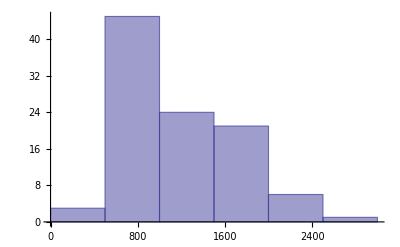

```mathematica
Histogram[{ComponentMeasurements[mCM,"Area"][[;;,2]] 2.5^2,ComponentMeasurements[mFB,"Area"][[;;,2]] 2.5^2}]
```

```mathematica
2.05^2/4.66
```

0.901824

```mathematica
Mean/@{(1-ComponentMeasurements[mCM,"Elongation"][[;;,2]])^-1,(1-ComponentMeasurements[mFB,"Elongation"][[;;,2]])^-1}
```

{1.85024,2.12496}

```mathematica
0.75 0.75
```

0.5625

```mathematica
0.1 0.03 14 14
```

0.588

```mathematica
CellDetect[arr_,n_]:=Map[If[#==n,1,0]&,arr,{2}];
```

```mathematica
CellSizeX[arr_]:=Module[{c=Total[arr]},Mean[c]];
```

```mathematica
cellNs=(Sort@DeleteDuplicates@Flatten@indexes)[[2;;100]]; cellN=Max[cellNs];
cellMasks=CellDetect[indexes,#]&/@cellNs;
cellImgs=ImageCrop[Image[1-cellMasks[[#]]]]&/@cellNs;
cellRSizes=ImageDimensions[cellImgs[[#]]]&/@cellNs;
```

```mathematica
cellImgs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cellSizes=Module[{dat=ImageData[cellImgs[[#]]]},{CellSizeX[datᵀ],CellSizeX[dat]}]&/@cellNs;
```

```mathematica
cellVolumes=Total[Flatten@cellMasks[[#]]]&/@cellNs;
```

```mathematica
{Mean[x],StandardDeviation[x],StandardDeviation[x]/Mean[x]}/.x->(cellRSizes[[;;,2]]/cellSizes[[;;,1]])
```

{4.83591,2.2757,0.470584}

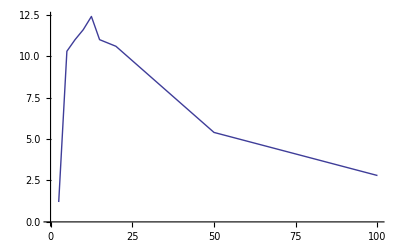

```mathematica
{{2.5,1.2},{5,10.3},{7.5,11},{10,11.6},{12.5,12.4},{15,11},{20,10.6},{50,5.4},{100,2.8}}//ListLinePlot
```

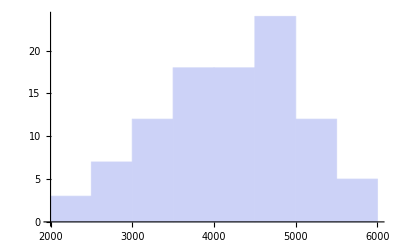

```mathematica
2.5^2 cellVolumes //Histogram
```

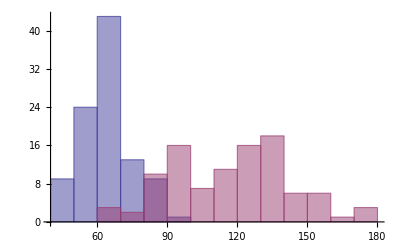

```mathematica
Histogram[2.5{cellRSizes[[;;,1]],cellRSizes[[;;,2]]},10]
```

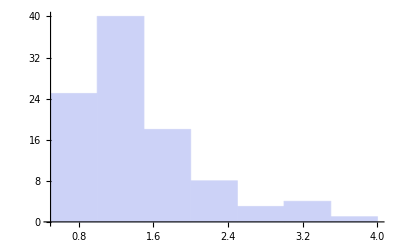

```mathematica
Histogram[cellRSizes[[;;,1]]/cellSizes[[;;,2]] ,5]
```

```mathematica
indexes=Import["./output/ctags900.out","Table"]ᵀ;
```

```mathematica
conts=Import["./output/contactM901.out","Table"]ᵀ;
```

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
cells=Map[ColorsReplace,indexes,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
outerConts=ArrayPad[Table[If[conts⟦i,j⟧==1,1-BorderQ[indexes,i,j],0],{i,2,Lx-1},{j,2,Ly-1}],1];
```

```mathematica
Image[ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]]
```

-Graphics-

```mathematica
{Lx,Ly}
```

{280,480}

```mathematica
data=Map[If[#>0&&types[[#]]==1,#,0]&,indexes,{2}];
```

```mathematica
contsI=conts;
```

```mathematica
σ=0; proc=0.3;Counts[arr_]:=Module[{uni=DeleteDuplicates[arr]},{Map[Count[arr,#]&,uni],uni}ᵀ];
Replacement[arr_]:=Module[{c=Counts[Flatten@arr]},Sort[c,#1[[1]]>#2[[1]]&]ᵀ[[2,1]]];
RepConts[arr_]:=If[Total[Flatten@arr]<(σ+1),0,1];
ContsW[arr_]:=Total[Flatten@arr]/(σ+1)^2;
```

```mathematica
If[σ==0,
indexes=data;
conts=contsI,
indexes=Table[Replacement[data[[i;;i+σ,j;;j+σ]]],{i,1,Dimensions[data][[1]]-σ,σ+1},{j,1,Dimensions[data][[2]]-σ,σ+1}];
conts=Table[RepConts[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
contsW=Table[ContsW[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
fibers=Table[RepConts[fibersI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[fibersI][[1]]-σ,σ+1},{j,1,Dimensions[fibersI][[2]]-σ,σ+1}]
];
```

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
cells=Map[ColorsReplace,indexes,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
outerConts=ArrayPad[Table[If[conts⟦i,j⟧==1,1-BorderQ[indexes,i,j],0],{i,2,Lx-1},{j,2,Ly-1}],1];
```

```mathematica
Image[ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]]
```

-Graphics-

```mathematica
vertBord=ArrayPad[Map[If[#≠0,1,0]&,indexes[[2;;]]-indexes[[;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[2;;]],{2}] Map[If[#≠0,1,0]&,indexes[[;;-2]],{2}],{{1,0},{0,0}}]ᵀ;vert=ArrayPad[Map[If[#==0,1,0]&,indexes[[2;;]]-indexes[[;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[2;;]],{2}],{{1,0},{0,0}}]ᵀ+2 vertBord;
```

```mathematica
horBord=ArrayPad[Map[If[#≠0,1,0]&,indexes[[;;,2;;]]-indexes[[;;, ;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[;;,2;;]],{2}] Map[If[#≠0,1,0]&,indexes[[;;, ;;-2]],{2}],{{0,0},{1,0}}]ᵀ;
hor=ArrayPad[Map[If[#==0,1,0]&,indexes[[;;,2;;]]-indexes[[;;, ;;-2]],{2}] Map[If[#≠0,1,0]&,indexes[[;;,2;;]],{2}],{{0,0},{1,0}}]ᵀ+2 horBord;
```

```mathematica
Image[((vertᵀ)~Join~(horᵀ))/2]
```

-Graphics-

```mathematica
Dimensions[contsW]
```

{280,480}

```mathematica
Dimensions[vert ]
```

{480,280}

```mathematica
Clear[Subscript[c, in],Subscript[c, L],Subscript[c, T]];
```

Clear::ssym: c_in is not a symbol or a string.

Clear::ssym: c_L is not a symbol or a string.

Clear::ssym: c_T is not a symbol or a string.

General::stop: Further output of Clear :: ssym will be suppressed during this calculation.

```mathematica
Subscript[c, in]=1; Subscript[c, L]=0.22; Subscript[c, T]=0.06;
```

```mathematica
vertR=(vert/.{2->Subscript[c, T],1->Subscript[c, in]})+vertBord contsᵀ (Subscript[c, L]-Subscript[c, T]);
horR=(hor/.{2->Subscript[c, T],1->Subscript[c, in]})+horBord contsᵀ(Subscript[c, L]-Subscript[c, T]);
```

```mathematica
Max[horR]
```

1.

```mathematica
DeleteDuplicates[Flatten@(Map[If[#≠0,1,0]&,horBord contsᵀ ,{2}]hor)]//N
```

{0.,2.}

```mathematica
TotalPar[arr_]:=If[Total[arr]==0,0,Times@@arr/Total[arr]];
FindRVert[arr_]:=Module[{c=Map[TotalPar,arr]},Total[c]]
```

```mathematica
(*horRsmall=ArrayPad[Table[FindRVert[horR⟦i;;i+dl-1,j-l1;;j+l2⟧],{i,1+l1,Ly-dl+1,dl},{j,1+l1,Lx-l2,dl}],{{1,0},{0,0}}];
vertRsmall=ArrayPad[Table[FindRVert[vertR⟦i-l1;;i+l2,j;;j+dl-1⟧ᵀ],{i,1+l1,Ly-l2,dl},{j,1+l1,Lx-dl+1,dl}],{{0,1},{1,0}}];
indexesRsmall=Table[indexes⟦j,i⟧,{i,1+l1,Ly,dl},{j,1+l1,Lx,dl}];*)
```

```mathematica
IfAny[arr_]:=If[Total[Flatten@arr]≠0,1,0];
IfHalf[arr_]:=If[Total[Flatten@arr]≥dl^2/2,1,0];
IfLine[arr_]:=If[Total[Flatten@arr]≥dl,1,0];
```

```mathematica
(*contsRsmall=ArrayPad[Table[IfLine@outerConts⟦j-l1;;j+l2,i-l1;;i+l2⟧,{i,1+l1,Ly-l2,dl},{j,1+l1,Lx-l2,dl}],{{1,0},{0,0}}];*)
```

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
niceCells=(ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]);
```

```mathematica
leaveX=32 7; leaveY =32 14; shiftx=-5;shifty=-5;
 cutX=Floor[(First@Dimensions[indexes]-leaveX)/2]+1;
cutY=Floor[(Last@Dimensions[indexes]-leaveY)/2]+1;
halfX=If[OddQ[First@Dimensions[indexes]-leaveX],1,0];
halfY=If[OddQ[Last@Dimensions[indexes]-leaveY],1,0];
Image[niceCells⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧]
```

-Graphics-

```mathematica
ind=indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧;
```

```mathematica
endsCut=conts⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
```

```mathematica
indCut=Map[If[#≠0,1,0]&,ind,{2}]ᵀ;
```

```mathematica
Dv=ArrayPad[vertRᵀ⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ,1];
Dh=ArrayPad[horRᵀ⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ,1];
```

```mathematica
{Lx,Ly}=Dimensions[Dv]-{2,2}
```

{448,224}

```mathematica
(*{Lx,Ly}={3,3};
Dv=Dh=ConstantArray[1,{5,5}];*)
```

```mathematica
X[i_]:=Mod[i-1,Lx]+1;
Y[i_]:=Floor[(i-1)/Lx]+1;
```

```mathematica
A=SparseArray[Table[{i,i}->-(Dh⟦X[i+1]+1,Y[i+1]+1⟧If[X[i]==Lx,0,1]+Dh⟦X[i]+1,Y[i]+1⟧If[X[i]==1,0,1]+Dv⟦X[i+Lx]+1,Y[i+Lx]+1⟧If[Y[i]==Ly,0,1]+Dv⟦X[i]+1,Y[i]+1⟧If[Y[i]==1,0,1]),{i,1,Lx Ly}]~Join~
Table[If[X[i]≠Lx,{i+1,i}-> Dh⟦X[i+1]+1,Y[i+1]+1⟧,{3,1}->0],{i,1,Lx Ly-1}]~Join~
Table[{i+Lx,i}->Dv⟦X[i+Lx]+1,Y[i+Lx]+1⟧,{i,1,Lx Ly-Lx}]];
```

```mathematica
Ar=ArrayRules[A];
```

```mathematica
Aint=Map[#[[1]]&,Ar][[;;-2]];
Areal=Map[#[[2]]&,Ar][[;;-2]];
```

```mathematica
Gather[Flatten@endsCut][[;;,1]]
```

{0,1}

```mathematica
Gather[Flatten@indCut][[;;,1]]
```

{0,1}

```mathematica
filename="./maps/cells.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@indCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(indCutᵀ),"Integer8"];Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/cells.bin"].

./maps/cells.bin

```mathematica
filename="./maps/A.bin";
DeleteFile[filename];
BinaryWrite[filename,{Lx,Ly,Length@(Flatten@Aint),Length@(Flatten@Areal)},"Integer32"]; 
BinaryWrite[filename,Flatten@Aint,"Integer32"];
BinaryWrite[filename,Flatten@Areal,"Real64"];Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/A.bin"].

./maps/A.bin

```mathematica
filename="./maps/na.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@endsCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(endsCutᵀ),"Integer8"]; Close[filename]
```

DeleteFile::nffil: File not found during DeleteFile["./maps/na.bin"].

./maps/na.bin

```mathematica
files=FileNames["../nrvm-discrete/test/*.png"];
filesT=FileNames["../nrvm-discrete/testT/*.png"];
```

```mathematica
mov=Import/@files;
movT=Import/@filesT;
```

```mathematica
dat=ImageData/@mov;
datT=ImageData/@movT;
```

```mathematica
Manipulate[ListPlot[{dat[[t,100,;;]],datT[[t,;;,100]]},PlotRange->{0,0.6}],{t,1,Min[Length@mov,Length@movT],1}]
```

Part::partw: Part 100 of {{0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, « 38 », 0.105882, 0.105882, 0.105882, 0.105882, 0.105882, « 46 »}, « 49 », « 46 »} does not exist.

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification dat ⟦ 1, 100, 1 ;; All ⟧ is longer than depth of object.

Part::partd: Part specification datT ⟦ 1, 1 ;; All, 100 ⟧ is longer than depth of object.

```mathematica
FindFront[arr_]:=Module[{c=Reverse@Map[If[#>0.3,1,0]&,arr]},Length@c-Position[c,1][[1,1]]]
```

```mathematica
front=FindFront[#[[150,;;]]]&/@dat;
frontT=FindFront[#[[;;,200]]]&/@datT;
```

Part::partw: Part 150 of {{0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, « 38 », 0.105882, 0.105882, 0.105882, 0.105882, 0.105882, « 46 »}, « 49 », « 46 »} does not exist.

Part::pspec: Part specification If[1 ;; All > 0.3, 1, 0] is neither an integer nor a list of integers.

Part::pspec: Part specification If[{{0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, « 39 », 0.105882, 0.105882, 0.105882, 0.105882, 0.105882, « 46 »}, « 49 », « 46 »} > 0.3, 1, 0] is neither an integer nor a list of integers.

Part::partw: Part 150 of {{0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.580392, « 38 », 0.105882, 0.105882, 0.105882, 0.105882, 0.105882, « 46 »}, « 49 », « 46 »} does not exist.

Part::pspec: Part specification If[1 ;; All > 0.3, 1, 0] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 150 of {{0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.588235, 0.572549, « 38 », 0.105882, 0.105882, 0.105882, 0.105882, 0.105882, « 46 »}, « 49 », « 46 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
ListPlot[{front[[;;Length@frontT]],frontT}]
```

ListPlot::lpn: {{}, {}} is not a list of numbers or pairs of numbers.

ListPlot[{{},{}}]

```mathematica
Export["./imgs/gif.gif",movT[[;;350]]]
```

Part::take: Cannot take positions 1 through 350 in {}.

./imgs/gif.gif

```mathematica
t1=10;t2=47; t3= t2;
vels={LinearModelFit[front[[t1;;t2]],x,x][[1,2,2]],LinearModelFit[frontT[[t1;;t3]],x,x][[1,2,2]]}(12.5 10^-4)/(50 10^-9 10^4)
```

Part::take: Cannot take positions 10 through 47 in {}.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

{-9.66046×10^-17,117.5}

```mathematica
vels[[1]]/vels[[2]]
```

-8.22166×10^-19

```mathematica
Image[Map[1-#&,borders,{2}]]
```

Image::imgarray: The specified argument borders should be an array of rank 2 or 3 with machine-sized numbers.

Image[borders]

```mathematica
σ=4; proc=0.3;Counts[arr_]:=Module[{uni=DeleteDuplicates[arr]},{Map[Count[arr,#]&,uni],uni}ᵀ];
Replacement[arr_]:=Module[{c=Counts[Flatten@arr]},Sort[c,#1[[1]]>#2[[1]]&]ᵀ[[2,1]]];
RepConts[arr_]:=If[Total[Flatten@arr]<(σ+1)^2 proc,0,1];
```

```mathematica
If[σ==0,
indexes=data;
conts=contsI,
indexes=Table[Replacement[data[[i;;i+σ,j;;j+σ]]],{i,1,Dimensions[data][[1]]-σ,σ+1},{j,1,Dimensions[data][[2]]-σ,σ+1}];
conts=Table[RepConts[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
fibers=Table[RepConts[fibersI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[fibersI][[1]]-σ,σ+1},{j,1,Dimensions[fibersI][[2]]-σ,σ+1}]
];
```